```mathematica
VectorPlot[{y,-x+0.1x^3},{x,-6,6},{y,-6,6},PlotLegends->Automatic,AspectRatio->0.8,Frame->True]//Rasterize
```

-Graphics-

```mathematica
Animate[VectorPlot[{y,-x+0.1x^3+3Sin[2Pi*t]},{x,-6,6},{y,-6,6},PlotLegends->Automatic,AspectRatio->0.8,Frame->True],{t,0,3}]
```

```mathematica
VectorPlot[{y,-Sin[x]},{x,-2Pi,2Pi},{y,-3,3},FrameLabel->{"θ","ω"},PlotLegends->Automatic,AspectRatio->0.8,Frame->True]//Rasterize
```

-Graphics-

```mathematica
plot=StreamPlot[{y,-Sin[x]},{x,-Pi,Pi},{y,-2,2},Frame->None,Epilog->{PointSize->Large,Point[{{0,0},{π,0},{-π,0}}]},StreamPoints->Fine,AspectRatio->0.8];
Show[First[Normal@plot]/.  a_Arrow:>(a/. {x_Real,y_Real}:>{Cos[x],Sin[x],y})//Graphics3D,Graphics3D@{Opacity@.7,LightBlue,Cylinder[{{0,0,-2},{0,0,2}}]}]
```

-Graphics3D-

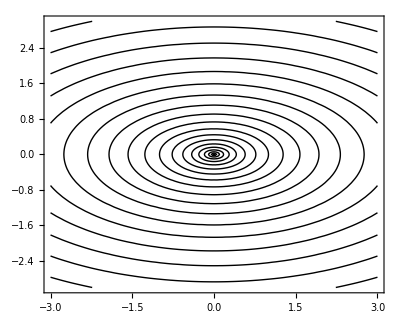

```mathematica
ContourPlot[x^2+3y^2,{x,-3,3},{y,-3,3},ContourShading->None,Contours->Table[i^5,{i,0,5,0.1}],AspectRatio->0.8]
```

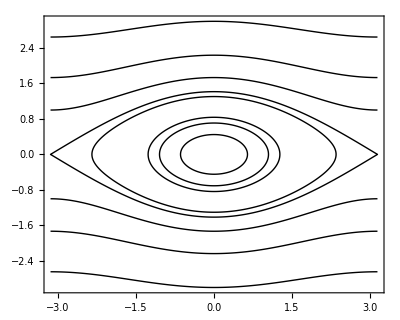

```mathematica
ContourPlot[y^2-Cos[x],{x,-Pi,Pi},{y,-3,3},ContourShading->None,Contours->{-1,1,0.7,-0.3,-0.8,-0.5,2,4,8},AspectRatio->0.8,PlotPoints->200]
```